## Data Handling

System & Directory

```mathematica
os = "win";
baselinux = "~/repos/fp/AFM";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.txt"];
```

Files listing

```mathematica
For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames⟦i⟧]]
```

1: 00-Referenzmessung-mit-Gitter Image 1.txt

2: 00-Referenzmessung-mit-Gitter Image 2.txt

3: 00-Referenzmessung-mit-Gitter Image 3.txt

4: 00-Referenzmessung-mit-Gitter Image 4.txt

5: 01-Gitter-schneller Image 1.txt

6: 01-Gitter-schneller Image 2.txt

7: 01-Gitter-schneller Image 3.txt

8: 01-Gitter-schneller Image 4.txt

9: 02-Gitter-sehr-langsam Image 1.txt

10: 02-Gitter-sehr-langsam Image 2.txt

11: 02-Gitter-sehr-langsam Image 3.txt

12: 02-Gitter-sehr-langsam Image 4.txt

13: 03-Gitter-ohne-P Image 1.txt

14: 03-Gitter-ohne-P Image 2.txt

15: 03-ZDUMMY Image 3.txt

16: 03-ZDUMMY Image 4.txt

17: 08-FP-1 Image 1.txt

18: 08-FP-1 Image 2.txt

19: 08-FP-1 Image 3.txt

20: 08-FP-1 Image 4.txt

21: 09-FP-1 Image 1.txt

22: 09-FP-1 Image 2.txt

23: 09-FP-1 Image 3.txt

24: 09-FP-1 Image 4.txt

25: 10-FP-3 Image 1.txt

26: 10-FP-3 Image 2.txt

27: 10-FP-3 Image 3.txt

28: 10-FP-3 Image 4.txt

29: 11-FP-3 Image 1.txt

30: 11-FP-3 Image 2.txt

31: 11-FP-3 Image 3.txt

32: 11-FP-3 Image 4.txt

33: 12-FP-3 Image 1.txt

34: 12-FP-3 Image 2.txt

35: 12-FP-3 Image 3.txt

36: 12-FP-3 Image 4.txt

37: 13-FP-4 Image 1.txt

38: 13-FP-4 Image 2.txt

39: 13-FP-4 Image 3.txt

40: 13-FP-4 Image 4.txt

41: 14-FP-7-Al Image 1.txt

42: 14-FP-7-Al Image 2.txt

43: 14-FP-7-Al Image 3.txt

44: 14-FP-7-Al Image 4.txt

45: 15-FP-7-Al Image 1.txt

46: 15-FP-7-Al Image 2.txt

47: 15-FP-7-Al Image 3.txt

48: 15-FP-7-Al Image 4.txt

49: 16-FP-7-Al Image 1.txt

50: 16-FP-7-Al Image 2.txt

51: 16-FP-7-Al Image 3.txt

52: 16-FP-7-Al Image 4.txt

53: 17-FP-2 Image 1.txt

54: 17-FP-2 Image 2.txt

55: 17-FP-2 Image 3.txt

56: 17-FP-2 Image 4.txt

57: 18-FP-5 Image 1.txt

58: 18-FP-5 Image 2.txt

59: 18-FP-5 Image 3.txt

60: 18-FP-5 Image 4.txt

Data generation

```mathematica
data[num_] := Drop[Import[fnames⟦num⟧, "Table"], 4];
```

## Analysis

#### Plot the different Images ‘res’ specifies the resolution, set to ‘1’ for full resolution ‘offset’ is 1 i --> image number - offset j --> real map or derrivative k --> determines scanning direction

```mathematica
res = 10; offset = 1;
Manipulate[{ListPlot3D[
					data[offset+4i+2k+j]⟦;; ;;res⟧,
					ColorFunction->"AvocadoColors",InterpolationOrder->1,ImageSize->1000,Mesh->None
					],
		 fnames[[offset+4i+2k+j]],
		  offset+4i+2k+j
		},
		{{i,0,Image Number},Range[0,(Length[fnames]-offset)/4]} ,
		{{j,1,"Type"},{1.0->"Height",0->"Derrivative"}},
		{{k,0,"Scanning Direction"},{0->"Forward",1.0->"Backward"}}
						]
```

TESTSECTION

```mathematica
ListPlot3D[data[50]⟦;; ;;10⟧,ColorFunction->"AvocadoColors",InterpolationOrder->1,ImageSize->1000,Mesh->None]
```

-Graphics3D-

```mathematica
datamatrix={data[50]⟦1⟧}
```

{{0.,0.,0.024881}}

```mathematica
data[50]⟦2⟧⟦2⟧== data[50]⟦1⟧⟦2⟧
```

True

```mathematica
data[50]⟦2⟧⟦1⟧
```

0.195555

```mathematica
data[50]⟦1⟧⟦1⟧
```

0.

```mathematica
If[data[50]⟦2⟧⟦2⟧== data[50]⟦1⟧⟦2⟧,datamatrix =Append[datamatrix,data[50]⟦2⟧] ]
```

{{0.,0.,0.024881},{0.195555,0.,0.0245933}}

```mathematica
datamatrix
```

{{0.,0.,0.024881}}

```mathematica
Length[data[50]]
```

65536

```mathematica
Sqrt[%]
```

256

```mathematica
data[50]
```

{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},{2.15111,0.,0.0238907},{2.34666,0.,0.0239137},{2.54222,0.,0.0242473},{2.73777,0.,0.0239596},{2.93333,0.,0.0239825},«65505»,{47.1288,49.995,0.00645198},{47.3244,49.995,0.00647492},{47.5199,49.995,0.0061872},{47.7155,49.995,0.00621014},{47.911,49.995,0.00623309},{48.1066,49.995,0.00625603},{48.3022,49.995,0.00627898},{48.4977,49.995,0.00599125},{48.6933,49.995,0.00570353},{48.8888,49.995,0.00541581},{49.0844,49.995,0.00512808},{49.2799,49.995,0.00515103},{49.4755,49.995,0.0048633},{49.671,49.995,0.00457558},{49.8666,49.995,0.00459852}}

```mathematica
data[50]⟦1;;256⟧
```

{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},{2.15111,0.,0.0238907},{2.34666,0.,0.0239137},{2.54222,0.,0.0242473},{2.73777,0.,0.0239596},{2.93333,0.,0.0239825},{3.12889,0.,0.0240054},{3.32444,0.,0.0240284},{3.52,0.,0.0240513},{3.71555,0.,0.0243849},{3.91111,0.,0.0244079},{4.10666,0.,0.0241202},{4.30222,0.,0.0244538},{4.49777,0.,0.0244767},{4.69333,0.,0.0244997},{4.88888,0.,0.0242119},{5.08444,0.,0.0242349},{5.27999,0.,0.0242578},{5.47555,0.,0.0239701},{5.6711,0.,0.0239931},{5.86666,0.,0.024016},{6.06221,0.,0.0237283},{6.25777,0.,0.0240619},{6.45333,0.,0.0237742},{6.64888,0.,0.0237971},{6.84444,0.,0.0235094},{7.03999,0.,0.0235323},{7.23555,0.,0.0232446},{7.4311,0.,0.0232675},{7.62666,0.,0.0232905},{7.82221,0.,0.0230028},{8.01777,0.,0.0233364},{8.21332,0.,0.0230487},{8.40888,0.,0.0233823},{8.60443,0.,0.0230945},{8.79999,0.,0.0231175},{8.99554,0.,0.0228298},{9.1911,0.,0.0231634},{9.38665,0.,0.022565},{9.58221,0.,0.0228986},{9.77777,0.,0.0229215},{9.97332,0.,0.0232552},{10.1689,0.,0.0232781},{10.3644,0.,0.0233011},{10.56,0.,0.023324},{10.7555,0.,0.0236576},{10.9511,0.,0.0236806},{11.1467,0.,0.0233928},{11.3422,0.,0.0234158},{11.5378,0.,0.0237494},{11.7333,0.,0.0234617},{11.9289,0.,0.0234846},{12.1244,0.,0.0235076},{12.32,0.,0.0235305},{12.5155,0.,0.0238641},{12.7111,0.,0.0238871},{12.9066,0.,0.0235993},{13.1022,0.,0.0239329},{13.2978,0.,0.0236452},{13.4933,0.,0.0236682},{13.6889,0.,0.0236911},{13.8844,0.,0.0237141},{14.08,0.,0.023737},{14.2755,0.,0.0237599},{14.4711,0.,0.0237829},{14.6666,0.,0.0241165},{14.8622,0.,0.0238288},{15.0578,0.,0.0238517},{15.2533,0.,0.0238747},{15.4489,0.,0.0232763},{15.6444,0.,0.0236099},{15.84,0.,0.0233222},{16.0355,0.,0.0233451},{16.2311,0.,0.0236787},{16.4266,0.,0.023391},{16.6222,0.,0.0237246},{16.8178,0.,0.0234369},{17.0133,0.,0.0234598},{17.2089,0.,0.0237934},{17.4044,0.,0.0238164},{17.6,0.,0.0238393},{17.7955,0.,0.0238623},{17.9911,0.,0.0235746},{18.1866,0.,0.0239082},{18.3822,0.,0.0239311},{18.5778,0.,0.0242647},{18.7733,0.,0.0242877},{18.9689,0.,0.0246213},{19.1644,0.,0.0243336},{19.36,0.,0.0243565},{19.5555,0.,0.0246901},{19.7511,0.,0.0244024},{19.9466,0.,0.0244253},{20.1422,0.,0.0244483},{20.3378,0.,0.0244712},{20.5333,0.,0.0244942},{20.7289,0.,0.0242064},{20.9244,0.,0.0245401},{21.12,0.,0.0242523},{21.3155,0.,0.0242753},{21.5111,0.,0.0242982},{21.7066,0.,0.0246318},{21.9022,0.,0.0243441},{22.0977,0.,0.0243671},{22.2933,0.,0.02439},{22.4889,0.,0.0247236},{22.6844,0.,0.0247466},{22.88,0.,0.0247695},{23.0755,0.,0.0247925},{23.2711,0.,0.0245047},{23.4666,0.,0.0245277},{23.6622,0.,0.0245506},{23.8577,0.,0.0251949},{24.0533,0.,0.0252178},{24.2489,0.,0.0252408},{24.4444,0.,0.0255744},{24.64,0.,0.0255973},{24.8355,0.,0.0256203},{25.0311,0.,0.0256432},{25.2266,0.,0.0256662},{25.4222,0.,0.0256891},{25.6177,0.,0.0260227},{25.8133,0.,0.0260457},{26.0089,0.,0.0260686},{26.2044,0.,0.0264022},{26.4,0.,0.0264252},{26.5955,0.,0.0264481},{26.7911,0.,0.0264711},{26.9866,0.,0.026494},{27.1822,0.,0.026517},{27.3777,0.,0.0265399},{27.5733,0.,0.0265629},{27.7689,0.,0.0265858},{27.9644,0.,0.0269194},{28.16,0.,0.0269424},{28.3555,0.,0.0269653},{28.5511,0.,0.0272989},{28.7466,0.,0.0273219},{28.9422,0.,0.0276555},{29.1377,0.,0.0276784},{29.3333,0.,0.0277014},{29.5288,0.,0.028035},{29.7244,0.,0.0277473},{29.92,0.,0.0277702},{30.1155,0.,0.0281038},{30.3111,0.,0.0281268},{30.5066,0.,0.0281497},{30.7022,0.,0.0281726},{30.8977,0.,0.0281956},{31.0933,0.,0.0285292},{31.2888,0.,0.0285521},{31.4844,0.,0.0282644},{31.68,0.,0.028598},{31.8755,0.,0.0289317},{32.0711,0.,0.0289546},{32.2666,0.,0.0292882},{32.4622,0.,0.0293112},{32.6577,0.,0.0293341},{32.8533,0.,0.029357},{33.0488,0.,0.02938},{33.2444,0.,0.0297136},{33.44,0.,0.0300472},{33.6355,0.,0.0303808},{33.8311,0.,0.0307144},{34.0266,0.,0.0307374},{34.2222,0.,0.0307603},{34.4177,0.,0.0310939},{34.6133,0.,0.0311169},{34.8088,0.,0.0311398},{35.0044,0.,0.0314734},{35.2,0.,0.0314964},{35.3955,0.,0.0312087},{35.5911,0.,0.0312316},{35.7866,0.,0.0312546},{35.9822,0.,0.0315882},{36.1777,0.,0.0316111},{36.3733,0.,0.0319447},{36.5688,0.,0.0319677},{36.7644,0.,0.0319906},{36.96,0.,0.0323242},{37.1555,0.,0.0326578},{37.3511,0.,0.0329915},{37.5466,0.,0.0330144},{37.7422,0.,0.0330373},{37.9377,0.,0.0330603},{38.1333,0.,0.0333939},{38.3288,0.,0.0334168},{38.5244,0.,0.0337505},{38.7199,0.,0.0337734},{38.9155,0.,0.034107},{39.1111,0.,0.03413},{39.3066,0.,0.0341529},{39.5022,0.,0.0341759},{39.6977,0.,0.0345095},{39.8933,0.,0.0348431},{40.0888,0.,0.0351767},{40.2844,0.,0.0355103},{40.4799,0.,0.0355333},{40.6755,0.,0.0355562},{40.8711,0.,0.0355791},{41.0666,0.,0.0359128},{41.2622,0.,0.0359357},{41.4577,0.,0.0359586},{41.6533,0.,0.0362923},{41.8488,0.,0.0363152},{42.0444,0.,0.0366488},{42.2399,0.,0.0366718},{42.4355,0.,0.0370054},{42.6311,0.,0.0367176},{42.8266,0.,0.0367406},{43.0222,0.,0.0370742},{43.2177,0.,0.0374078},{43.4133,0.,0.0374308},{43.6088,0.,0.0377644},{43.8044,0.,0.038098},{43.9999,0.,0.0381209},{44.1955,0.,0.0384545},{44.3911,0.,0.0384775},{44.5866,0.,0.0385004},{44.7822,0.,0.0385234},{44.9777,0.,0.0385463},{45.1733,0.,0.0385693},{45.3688,0.,0.0389029},{45.5644,0.,0.0389258},{45.7599,0.,0.0392594},{45.9555,0.,0.0392824},{46.151,0.,0.0393053},{46.3466,0.,0.0396389},{46.5422,0.,0.0396619},{46.7377,0.,0.0396848},{46.9333,0.,0.0400184},{47.1288,0.,0.0400414},{47.3244,0.,0.0400643},{47.5199,0.,0.0400873},{47.7155,0.,0.0401102},{47.911,0.,0.0401332},{48.1066,0.,0.0401561},{48.3022,0.,0.0404897},{48.4977,0.,0.041134},{48.6933,0.,0.041157},{48.8888,0.,0.0411799},{49.0844,0.,0.0412028},{49.2799,0.,0.0415365},{49.4755,0.,0.0415594},{49.671,0.,0.0415823},{49.8666,0.,0.0416053}}

```mathematica
Zeilenlaenge=256;
datamatrix=Table[data[50]⟦1+i*Zeilenlaenge;;Zeilenlaenge*(1+i)⟧,{i,0,Zeilenlaenge-1}]
```

{{{0.,0.,0.024881},{0.195555,0.,0.0245933},{0.391111,0.,0.0246162},{0.586666,0.,0.0243285},{0.782221,0.,0.0243514},{0.977776,0.,0.0240637},{1.17333,0.,0.0240867},{1.36889,0.,0.0241096},{1.56444,0.,0.0241326},{1.76,0.,0.0238448},{1.95555,0.,0.0238678},{2.15111,0.,0.0238907},{2.34666,0.,0.0239137},{2.54222,0.,0.0242473},{2.73777,0.,0.0239596},{2.93333,0.,0.0239825},{3.12889,0.,0.0240054},«222»,{46.7377,0.,0.0396848},{46.9333,0.,0.0400184},{47.1288,0.,0.0400414},{47.3244,0.,0.0400643},{47.5199,0.,0.0400873},{47.7155,0.,0.0401102},{47.911,0.,0.0401332},{48.1066,0.,0.0401561},{48.3022,0.,0.0404897},{48.4977,0.,0.041134},{48.6933,0.,0.041157},{48.8888,0.,0.0411799},{49.0844,0.,0.0412028},{49.2799,0.,0.0415365},{49.4755,0.,0.0415594},{49.671,0.,0.0415823},{49.8666,0.,0.0416053}},«254»,{«1»}}

```mathematica
datamatrix⟦1⟧⟦2⟧
```

{0.195555,0.,0.0245933}

```mathematica
datamatrix⟦2⟧⟦1⟧
```

{0.,0.196059,0.0202415}

```mathematica
datamatrix⟦1⟧⟦1⟧
```

{0.,0.,0.024881}

```mathematica
v1=datamatrix⟦1+1⟧⟦1⟧-datamatrix⟦1⟧⟦1⟧
```

{0.,0.196059,-0.0046395}

```mathematica
v2=datamatrix⟦1⟧⟦2⟧-datamatrix⟦1⟧⟦1⟧
```

{0.195555,0.,-0.0002877}

```mathematica
<<VectorAnalysis`
```

```mathematica
CrossProduct[{0,0,1},{1,0,0}]
```

{0,1,0}

```mathematica
a= {1,3,5}
```

{1,3,5}

```mathematica
b={-4, 7,1}
```

{-4,7,1}

```mathematica
CrossProduct[a, b]
```

{-32,-21,19}

```mathematica
Abs[CrossProduct[v1, v2]]
```

{0.0000564062,0.000907277,0.0383403}

```mathematica
Cross[v1,v2]
```

{-0.0000564062,-0.000907277,-0.0383403}

```mathematica
Norm[v1×v2]
```

0.0383511

```mathematica
0.195555^2
```

0.0382418

```mathematica
i=1; k=1;
Norm[(datamatrix⟦k⟧⟦i+1⟧-datamatrix⟦k⟧⟦i⟧)×(datamatrix⟦k+1⟧⟦i⟧-datamatrix⟦k⟧⟦i⟧)]/2
```

0.0191755

```mathematica
dd=Norm[(datamatrix⟦1+1⟧⟦1⟧-datamatrix⟦1⟧⟦1⟧)×(datamatrix⟦1⟧⟦2⟧-datamatrix⟦1⟧⟦1⟧)]/2
```

0.0191755

```mathematica
Ad=0;Au=0;Zeilenlaenge=256;
For[i=1, i<Zeilenlaenge-1,
	For[k=1, k<Zeilenlaenge-1,
Ad+=Norm[(datamatrix⟦k⟧⟦i+1⟧-datamatrix⟦k⟧⟦i⟧)×(datamatrix⟦k+1⟧⟦i⟧-datamatrix⟦k⟧⟦i⟧)]/2;
Au+=Norm[(datamatrix⟦k⟧⟦i+1⟧-datamatrix⟦k+1⟧⟦i+1⟧)×(datamatrix⟦k+1⟧⟦i⟧-datamatrix⟦k+1⟧⟦i+1⟧)]/2
;k+=1];
i+=1];
A=Ad+Au
Print[NumberForm[Ad,10]];
Print[Au];
```

1236.800681

1236.8

```mathematica
NumberForm[Au,10]
```

1236.800695

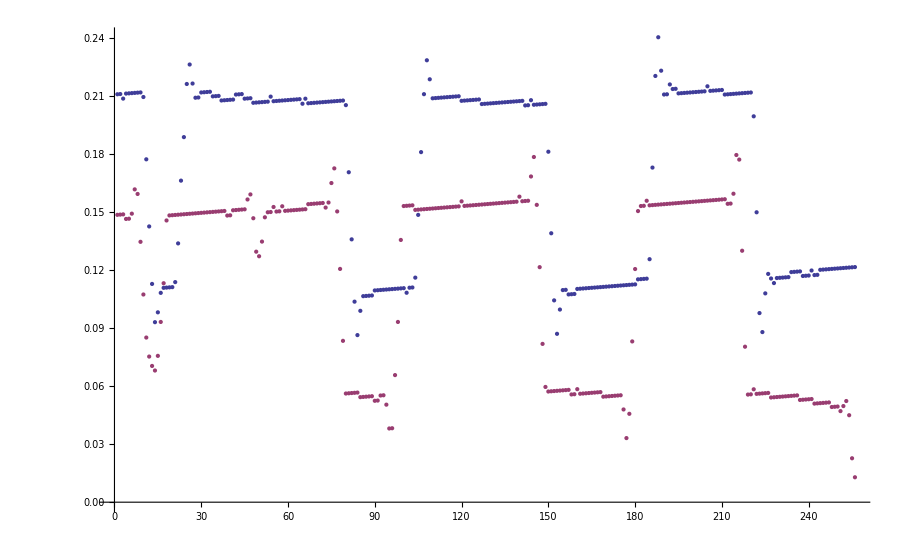

```mathematica
ListPlot[{data[2]⟦1;;256⟧⟦All,3⟧,data[4]⟦1;;256⟧⟦All,3⟧}]
```

```mathematica
diff=data[2]⟦1;;256⟧⟦All,3⟧-data[4]⟦1;;256⟧⟦All,3⟧;
```

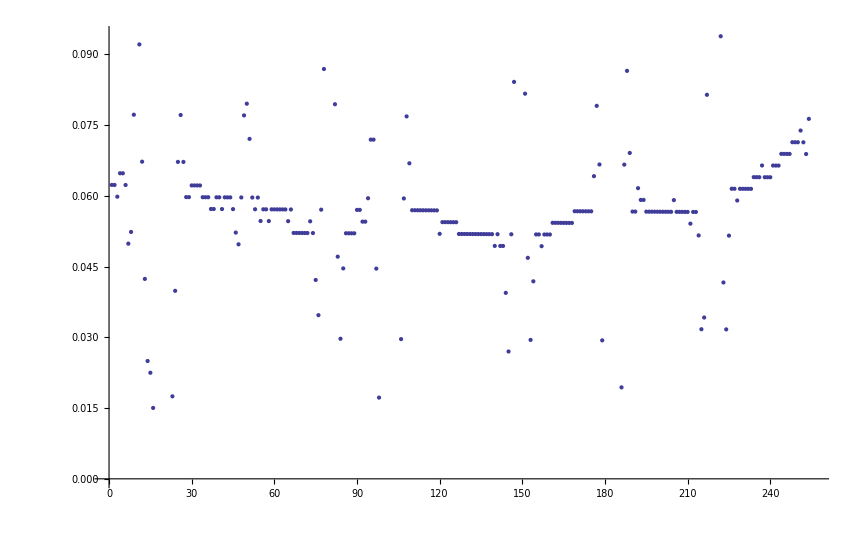

```mathematica
ListPlot[diff]
```

```mathematica
forward=Drop[Import["D:\\Git\\F-Praktikum\\AFM\\bearbeitete_scans\\16-FP-7-Al Image 2.txt","Table"],4]
```

{{0.,0.,0.00803958},{0.195555,0.,0.00759315},{0.391111,0.,0.00753938},{0.586666,0.,0.00709623},{0.782221,0.,0.0070844},{0.977776,0.,0.00677346},{1.17333,0.,0.00679774},{1.36889,0.,0.00693734},{1.56444,0.,0.00709846},{1.76,0.,0.00702333},{1.95555,0.,0.00721654},«65514»,{47.911,49.995,0.00701131},{48.1066,49.995,0.00714764},{48.3022,49.995,0.00728466},{48.4977,49.995,0.00708224},{48.6933,49.995,0.00691435},{48.8888,49.995,0.00665976},{49.0844,49.995,0.00647732},{49.2799,49.995,0.00661329},{49.4755,49.995,0.00636019},{49.671,49.995,0.00617175},{49.8666,49.995,0.00623678}}

```mathematica
backward=Drop[Import["D:\\Git\\F-Praktikum\\AFM\\bearbeitete_scans\\16-FP-7-Al Image 4.txt","Table"],4]
```

{{0.,0.,0.00198253},{0.195555,0.,0.00239997},{0.391111,0.,0.00249156},{0.586666,0.,0.00263314},{0.782221,0.,0.00253088},{0.977776,0.,0.00306769},{1.17333,0.,0.00290595},{1.36889,0.,0.00274639},{1.56444,0.,0.00290409},{1.76,0.,0.00278416},{1.95555,0.,0.00272716},«65514»,{47.911,49.995,0.00229862},{48.1066,49.995,0.00232189},{48.3022,49.995,0.00250624},{48.4977,49.995,0.00187398},{48.6933,49.995,0.0018809},{48.8888,49.995,0.00156775},{49.0844,49.995,0.00154383},{49.2799,49.995,0.00136886},{49.4755,49.995,0.00140161},{49.671,49.995,0.00127232},{49.8666,49.995,0.00135472}}

```mathematica
Zeile =60; Zeilen=10;
```

```mathematica
Manipulate[ListPlot[{forward⟦1+256*Zeile;;Zeilen*256+256*Zeile⟧⟦All,3⟧,backward⟦1+256*Zeile;;Zeilen*256+256*Zeile⟧⟦All,3⟧+dy}, PlotRange->{0.002,0.01}]
,{dy,0,0.007}]
```

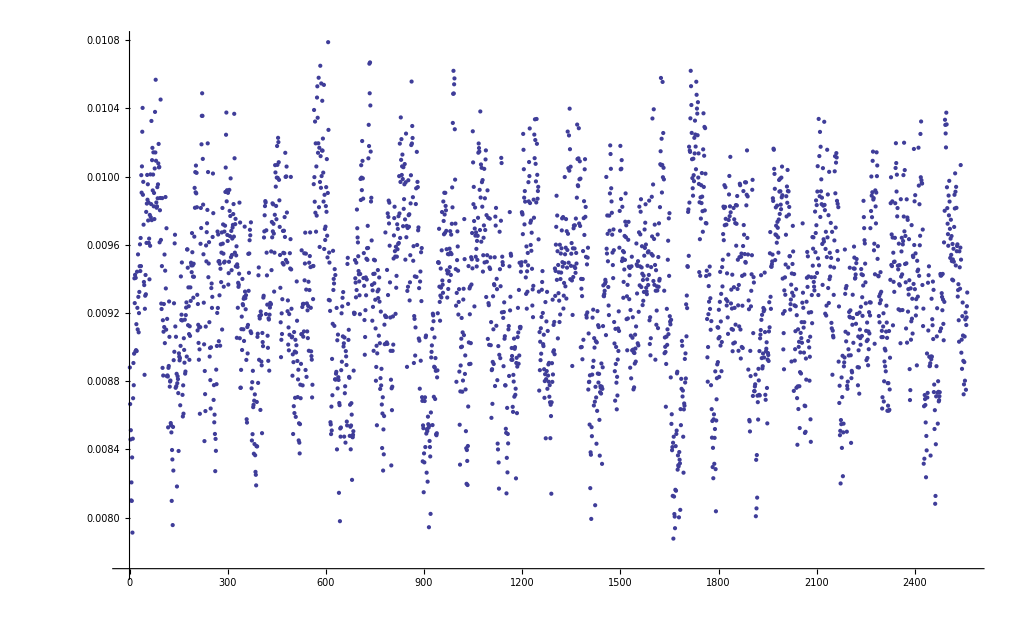

```mathematica
ListPlot[{forward⟦1+256*Zeile;;Zeilen*256+256*Zeile⟧⟦All,3⟧-backward⟦1+256*Zeile;;Zeilen*256+256*Zeile⟧⟦All,3⟧+0.00468}]
```

```mathematica
DiscreteConvolve[forward⟦n⟧⟦3⟧,backward⟦n⟧⟦3⟧,n,m]
```

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ does not exist.

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00198253}, {0.195555, 0., 0.00239997}, {0.391111, 0., 0.00249156}, {0.586666, 0., 0.00263314}, {0.782221, 0., 0.00253088}, {0.977776, 0., 0.00306769}, {1.17333, 0., 0.00290595}, {1.36889, 0., 0.00274639}, {1.56444, 0., 0.00290409}, {1.76, 0., 0.00278416}, {1.95555, 0., 0.00272716}, {2.15111, 0., 0.00266466}, {2.34666, 0., 0.00284995}, {2.54222, 0., 0.00273801}, {2.73777, 0., 0.00269887}, {2.93333, 0., 0.0028422}, {3.12889, 0., 0.00269577}, {3.32444, 0., 0.00258492}, {3.52, 0., 0.00254278}, « 13 », {6.25777, 0., 0.00259159}, {6.45333, 0., 0.00249806}, {6.64888, 0., 0.00247366}, {6.84444, 0., 0.00259669}, {7.03999, 0., 0.00221319}, {7.23555, 0., 0.00217322}, {7.4311, 0., 0.0023656}, {7.62666, 0., 0.00205307}, {7.82221, 0., 0.00228685}, {8.01777, 0., 0.00220739}, {8.21332, 0., 0.00190968}, {8.40888, 0., 0.00194094}, {8.60443, 0., 0.00226193}, {8.79999, 0., 0.00187029}, {8.99554, 0., 0.00219001}, {9.1911, 0., 0.00245959}, {9.38665, 0., 0.00266807}, {9.58221, 0., 0.00228852}, « 65486 »} ⟦ n ⟧ does not exist.

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ does not exist.

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00198253}, {0.195555, 0., 0.00239997}, {0.391111, 0., 0.00249156}, {0.586666, 0., 0.00263314}, {0.782221, 0., 0.00253088}, {0.977776, 0., 0.00306769}, {1.17333, 0., 0.00290595}, {1.36889, 0., 0.00274639}, {1.56444, 0., 0.00290409}, {1.76, 0., 0.00278416}, {1.95555, 0., 0.00272716}, {2.15111, 0., 0.00266466}, {2.34666, 0., 0.00284995}, {2.54222, 0., 0.00273801}, {2.73777, 0., 0.00269887}, {2.93333, 0., 0.0028422}, {3.12889, 0., 0.00269577}, {3.32444, 0., 0.00258492}, {3.52, 0., 0.00254278}, « 13 », {6.25777, 0., 0.00259159}, {6.45333, 0., 0.00249806}, {6.64888, 0., 0.00247366}, {6.84444, 0., 0.00259669}, {7.03999, 0., 0.00221319}, {7.23555, 0., 0.00217322}, {7.4311, 0., 0.0023656}, {7.62666, 0., 0.00205307}, {7.82221, 0., 0.00228685}, {8.01777, 0., 0.00220739}, {8.21332, 0., 0.00190968}, {8.40888, 0., 0.00194094}, {8.60443, 0., 0.00226193}, {8.79999, 0., 0.00187029}, {8.99554, 0., 0.00219001}, {9.1911, 0., 0.00245959}, {9.38665, 0., 0.00266807}, {9.58221, 0., 0.00228852}, « 65486 »} ⟦ n ⟧ does not exist.

DiscreteConvolve[{{0.,0.,0.00803958},{0.195555,0.,0.00759315},{0.391111,0.,0.00753938},{0.586666,0.,0.00709623},{0.782221,0.,0.0070844},{0.977776,0.,0.00677346},{1.17333,0.,0.00679774},{1.36889,0.,0.00693734},{1.56444,0.,0.00709846},{1.76,0.,0.00702333},{1.95555,0.,0.00721654},{2.15111,0.,0.00734714},{2.34666,0.,0.00744562},{2.54222,0.,0.00775857},{2.73777,0.,0.0073964},{2.93333,0.,0.00741887},{3.12889,0.,0.00739018},«65502»,{46.7377,49.995,0.00664734},{46.9333,49.995,0.00676672},{47.1288,49.995,0.00690284},{47.3244,49.995,0.00706617},{47.5199,49.995,0.0068238},{47.7155,49.995,0.00693798},{47.911,49.995,0.00701131},{48.1066,49.995,0.00714764},{48.3022,49.995,0.00728466},{48.4977,49.995,0.00708224},{48.6933,49.995,0.00691435},{48.8888,49.995,0.00665976},{49.0844,49.995,0.00647732},{49.2799,49.995,0.00661329},{49.4755,49.995,0.00636019},{49.671,49.995,0.00617175},{49.8666,49.995,0.00623678}}⟦n⟧⟦3⟧,«2»,m]

```mathematica
f[n_]:=forward⟦n⟧⟦3⟧;b[n_]:=forward⟦n⟧⟦3⟧;
```

```mathematica
DiscreteConvolve[f[n],b[n],n,m]
```

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ does not exist.

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ does not exist.

$Aborted

```mathematica
ListPlot[f[n],{n,1,5}]
```

Part::pspec: Part specification n is neither an integer nor a list of integers.

Part::partw: Part 3 of {{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ does not exist.

ListPlot::nonopt: Options expected (instead of {n, 1, 5}) beyond position 1 in ListPlot[{{0., 0., 0.00803958}, {0.195555, 0., 0.00759315}, {0.391111, 0., 0.00753938}, {0.586666, 0., 0.00709623}, {0.782221, 0., 0.0070844}, {0.977776, 0., 0.00677346}, {1.17333, 0., 0.00679774}, {1.36889, 0., 0.00693734}, {1.56444, 0., 0.00709846}, {1.76, 0., 0.00702333}, {1.95555, 0., 0.00721654}, {2.15111, 0., 0.00734714}, {2.34666, 0., 0.00744562}, {2.54222, 0., 0.00775857}, {2.73777, 0., 0.0073964}, {2.93333, 0., 0.00741887}, {3.12889, 0., 0.00739018}, {3.32444, 0., 0.00742664}, {3.52, 0., 0.00738516}, « 13 », {6.25777, 0., 0.00744706}, {6.45333, 0., 0.00726811}, {6.64888, 0., 0.00732168}, {6.84444, 0., 0.00710039}, {7.03999, 0., 0.0071177}, {7.23555, 0., 0.00688246}, {7.4311, 0., 0.00691531}, {7.62666, 0., 0.00689129}, {7.82221, 0., 0.00661802}, {8.01777, 0., 0.00690999}, {8.21332, 0., 0.00665535}, {8.40888, 0., 0.00689295}, {8.60443, 0., 0.00650414}, {8.79999, 0., 0.00658213}, {8.99554, 0., 0.0062759}, {9.1911, 0., 0.00654053}, {9.38665, 0., 0.00591553}, {9.58221, 0., 0.00628565}, « 65486 »} ⟦ n ⟧ ⟦ 3 ⟧, {n, 1, 5}]. An option must be a rule or a list of rules.

ListPlot[{{0.,0.,0.00803958},{0.195555,0.,0.00759315},{0.391111,0.,0.00753938},{0.586666,0.,0.00709623},{0.782221,0.,0.0070844},{0.977776,0.,0.00677346},{1.17333,0.,0.00679774},{1.36889,0.,0.00693734},{1.56444,0.,0.00709846},{1.76,0.,0.00702333},{1.95555,0.,0.00721654},{2.15111,0.,0.00734714},{2.34666,0.,0.00744562},{2.54222,0.,0.00775857},{2.73777,0.,0.0073964},{2.93333,0.,0.00741887},{3.12889,0.,0.00739018},«65502»,{46.7377,49.995,0.00664734},{46.9333,49.995,0.00676672},{47.1288,49.995,0.00690284},{47.3244,49.995,0.00706617},{47.5199,49.995,0.0068238},{47.7155,49.995,0.00693798},{47.911,49.995,0.00701131},{48.1066,49.995,0.00714764},{48.3022,49.995,0.00728466},{48.4977,49.995,0.00708224},{48.6933,49.995,0.00691435},{48.8888,49.995,0.00665976},{49.0844,49.995,0.00647732},{49.2799,49.995,0.00661329},{49.4755,49.995,0.00636019},{49.671,49.995,0.00617175},{49.8666,49.995,0.00623678}}⟦n⟧⟦3⟧,{n,1,5}]

```mathematica
f[n_]=forward⟦1+256*Zeile;;Zeilen*256+256*Zeile⟧⟦All,3⟧⟦1⟧
```

Set::write: Tag List in {0.00658914, 0.00664251, 0.00641096, 0.00646271, 0.00623905, 0.00628739, 0.00637362, 0.00653284, 0.00631403, 0.00677384, 0.0069284, 0.00704724, 0.00681889, 0.00690963, 0.00727992, 0.007031, 0.00712204, 0.00688464, 0.00725721, 0.00703704, 0.00711742, 0.00716553, 0.0075273, 0.00725834, 0.00736516, 0.00742747, 0.00713179, 0.00688283, 0.00695154, 0.00701013, 0.00708612, 0.00713993, 0.00689692, 0.00699068, 0.00705168, 0.0071471, 0.0072384, 0.00731629, 0.00738409, 0.00743535, 0.00716487, 0.00721583, 0.00725373, 0.00726534, 0.00726923, 0.00701178, 0.00705304, 0.00705589, 0.00710059, 0.00720575, « 2510 »}[n_] is Protected.

0.00658914